```mathematica
a=Import["G:\\calc-online\\gpd\\k-result\\diagram-n-n-he-delta.wdx"];
f1=Query[1,1]@a;
g1=Query[1,2]@a;
f2=Query[2,1]@a;
g2=Query[2,2]@a;
f3=Query[3,1]@a;
g3=Query[3,2]@a;

f12=f1/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
f22=f2/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
f32=f3/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};

g12=g1/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g22=g2/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g32=g3/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
```

```mathematica
nf12=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->1,P1->1,Q->1};
nf22=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->1,P1->1,Q->1};
nf32=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->1,P1->1,Q->1,y->0,M->0.1381};

nf1=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1};
nf2=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1};
nf3=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1,y->0,M->0.1381};
```

```mathematica
ng12=g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->1,P1->1,Q->1};
ng22=g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->1,P1->1,Q->1};
ng32=g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->1,P1->1,Q->1,y->0,M->0.1381};

ng1=g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1};
ng2=g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1};
ng3=g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1,y->0,M->0.1381};
```

```mathematica
NIntegrate[nf12,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf22,{y,1-0.2,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

2.973151515 ⅈ

```mathematica
NIntegrate[nf1,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf2,{y,1-0.1,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

2.97314649 ⅈ

```mathematica
NIntegrate[ng12,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng22,{y,1-0.2,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.38452702 ⅈ

```mathematica
NIntegrate[ng1,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng2,{y,1-0.1,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.38452686 ⅈ

```mathematica
Denominator[nf3t]
```

k1 (0.99-2. k1+k1^2)^2 (1.+k3^2-0.980928 x)^3

```mathematica
NIntegrate[nf3s,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-0.3024971984 ⅈ

```mathematica
NIntegrate[nf4s,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.677602785 ⅈ

```mathematica
NIntegrate[nf4s2,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.783895022 ⅈ

```mathematica
NIntegrate[nf3s2,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-0.3474932225 ⅈ

```mathematica
-1.4884748394000342148965417072590931418`10. ⅈ-1.78389502152959767751918374207486494326`10. ⅈ
```

-3.272369861 ⅈ

```mathematica
-1.67760278539546659826372752319214194867`10. ⅈ-1.58633975056833148422743153018980571886`10. ⅈ
```

-3.263942536 ⅈ

```mathematica
nf13=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->1,P1->1,Q->1};
nf23=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->1,P1->1,Q->1};
nf33=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->1,P1->1,Q->1};
nf43=f42/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->1,P1->1,Q->1};
nf3t3=Together[nf33];
nf3s3=Cancel[Simplify[(Numerator[nf3t3]-Coefficient[Numerator[nf3t3],k1,0])]/Denominator[nf3t3]]/.{k1->0};
nf4s3=Simplify[nf43]/.{k1->0};
nf14=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->1,P1->1,Q->1};
nf24=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->1,P1->1,Q->1};
nf34=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->1,P1->1,Q->1};
nf44=f42/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->1,P1->1,Q->1};
nf3t4=Together[nf34];
nf3s4=Cancel[Simplify[(Numerator[nf3t4]-Coefficient[Numerator[nf3t4],k1,0])]/Denominator[nf3t4]]/.{k1->0};
nf4s4=Simplify[nf44]/.{k1->0};
```

```mathematica
NIntegrate[nf13,{y,0,1-0.3},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf23,{y,1-0.3,1+0.3},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf4s3,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.285654845 ⅈ

```mathematica
NIntegrate[nf14,{y,0,1-0.4},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf24,{y,1-0.4,1+0.4},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf4s4,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.285387644 ⅈ

```mathematica
nf1[y_]=Simplify[f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1}];
nf2[y_]=Simplify[f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1}];
nf3=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1,y->0,M->0.1381};
ng1[y_]=Simplify[g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1}];
ng2[y_]=Simplify[g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1}];
ng3=g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->1,P1->1,Q->1,y->0,M->0.1381};
```

```mathematica
inf1[y_]:=NIntegrate[nf1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing1[y_]:=NIntegrate[ng1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
inf2[y_]:=NIntegrate[nf2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing2[y_]:=NIntegrate[ng2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
lf1=ParallelTable[{y,inf1[y]},{y,0,0.9,0.01}];
lg1=ParallelTable[{y,ing1[y]},{y,0,0.9,0.01}];
lf2=ParallelTable[{y,inf2[y]},{y,0.9,1.1,0.01}];
lg2=ParallelTable[{y,ing2[y]},{y,0.9,1.1,0.01}];
```

```mathematica
sf1=Interpolation[lf1];
sf2=Interpolation[lf2];
sg1=Interpolation[lg1];
sg2=Interpolation[lg2];
```

```mathematica
pathf101=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"n-f1-0.1.pdf"}];
Export[pathf101,Labeled[Show[Plot[I*sf1[x],{x,0,0.9},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[I*sf2[x],{x,0.9,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,n],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\n-f1-0.1.pdf

```mathematica
pathg101=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"n-g1-0.1.pdf"}];
Export[pathg101,Labeled[Show[Plot[I*sg1[x],{x,0,0.9},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[I*sg2[x],{x,0.9,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,n],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\n-g1-0.1.pdf

```mathematica
SystemOpen["G:\\output\\summary\\gpd\\pic\\n-g1-0.1.pdf"]
```

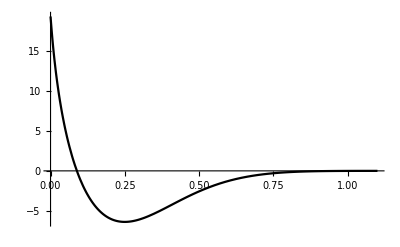
-Graphics-f_nyξ=0.1

```mathematica
Labeled[Show[Plot[I*sf1[x],{x,0,0.9},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[I*sf2[x],{x,0.9,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,n],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

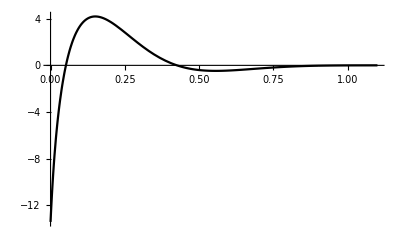
-Graphics-g_nyξ=0.1

```mathematica
Labeled[Show[Plot[I*sg1[x],{x,0,0.9},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[I*sg2[x],{x,0.9,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,n],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```